```mathematica
thz2waavenum=1/0.0299792458;SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/cvac_phon_dos"];
cvac=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
names2={"Perfet Zr32C32","Frenkel Zr32C32 -- Bound Dimer","Frenkel Zr32C32 -- Bound Trimer","Frenkel Zr32C32 -- Unbound Dimer","Frenkel Zr32C32 -- Unbound Trimer","Frenkel Zr32C32 -- Unbound Tetramer","CVAC Zr32C31 - 3 C at. %"};
(*names={"perf","fren129","fren142","fren70","fren174","fren1126","cvac"};
objects={perf,fren129,fren142,fren70,fren174,fren1126,cvac};*)
names={"fren129","fren142","fren70","fren174","fren1126"};
objects={fren129,fren142,fren70,fren174,fren1126};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
fren1126Data=Table[Table[Flatten[{(fren1126[[j]][[i]][[1]]*thz2waavenum),vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

```mathematica
data2D//Dimensions
```

{5,11,203,2}

```mathematica
alatts
```

{4.575,4.6,4.625,4.6583,4.685,4.73,4.759,4.801,4.85,4.875,4.9}

```mathematica
Length[{4.575,4.6,4.625,4.6583,4.685,4.73,4.759,4.801,4.85,4.875,4.9}]
```

11

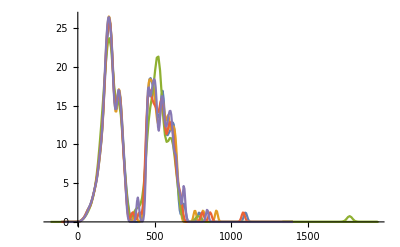

```mathematica
ListLinePlot@Table[data2D[[i]][[5]],{i,1,Length@data2D}]
```

```mathematica
data2Dint=Table[Table[Interpolation[data2D[[i]][[vol]]],{vol,1,Length@data2D[[1]]}],{i,1,Length@data2D}];
data2Dtab=Table[Table[Table[{x,data2Dint[[i]][[vol]][x]},{x,0,data2D[[i]][[vol]][[-1]][[1]],1}],{vol,1,Length@data2D[[1]]}],{i,1,Length@data2D}];
```

```mathematica
dataT=Transpose[data2Dtab[[2]][[3]]][[2]];
data =data2Dtab[[2]][[3]];
```

```mathematica
data2Dtab//Dimensions
```

{5,11,1401,2}

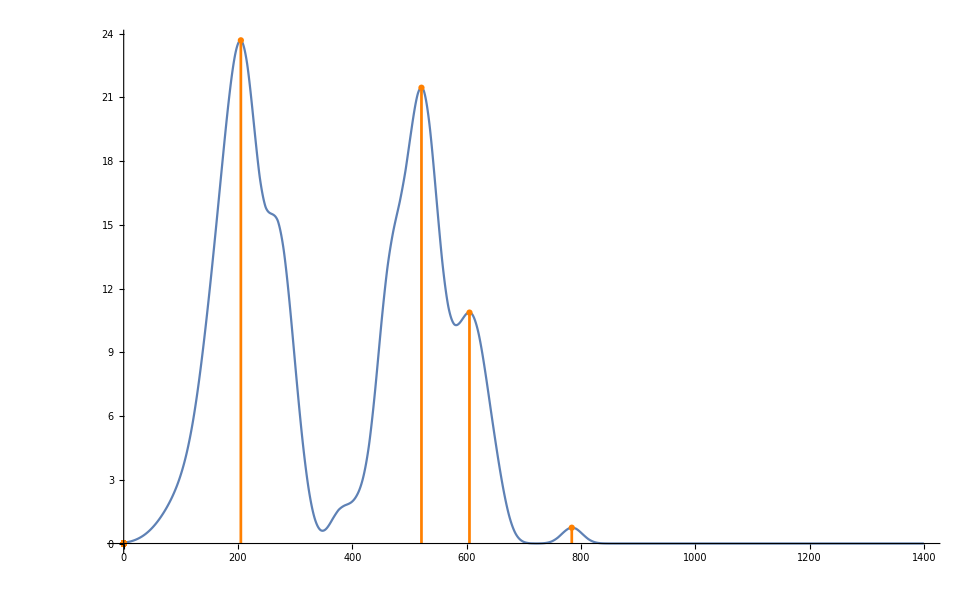

```mathematica
Show[{ListLinePlot[data2Dtab[[3]][[5]],PlotRange->All],ListPlot[data2Dtab[[3]][[5]] PeakDetect[Transpose[data2Dtab[[3]][[5]]][[2]],0,0,0.5],Filling->Bottom,FillingStyle->Thickness[0.002],PlotStyle->Directive[Orange]]}]
```

```mathematica
DeleteCases[data2Dtab[[2]][[3]] PeakDetect[Transpose[data2Dtab[[2]][[3]]][[2]],1,0,0.5],x_/;x[[1]]<0.1]
```

{{217,26.1255},{285,16.9397},{405,1.4439},{501,18.9195},{582,16.0699},{617,13.6461},{791,1.44405},{845,1.43732},{920,1.43665}}

```mathematica
data2Dtab//Dimensions
```

{5,11,1401,2}

```mathematica
peaks=Table[Table[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],0,0,0.01],x_/;x[[1]]<0.1],{vol,1,9}],{type,1,5}];
peaks2=Table[Table[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],0,0,0.01],x_/;x[[1]]<0.1],{type,1,5}],{vol,1,9}];
```

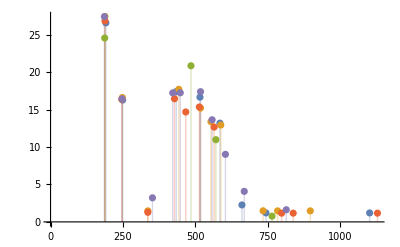

```mathematica
ListPlot[peaks2[[7]],Filling->Bottom]
```

```mathematica
peaksDefects=Table[Table[DeleteCases[DeleteCases[data2Dtab[[type]][[vol]] PeakDetect[Transpose[data2Dtab[[type]][[vol]]][[2]],9,0,0.1],x_/;x[[1]]<0.1],x_/;x[[2]]>6],{type,1,5}],{vol,1,11}];
```

{11,5}

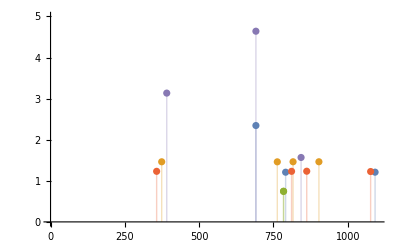

```mathematica
peaksDefects//Dimensions
ListPlot[peaksDefects[[5]],Filling->Bottom,PlotRange->{{0,1100},{0,5}}]
```

```mathematica
defectFreqs=Table[Transpose[peaksDefects[[5]][[i]]][[1]],{i,1,5}]
```

{{691,791,1092},{374,763,816,903},{784},{357,811,862,1077},{391,691,843}}

```mathematica
Flatten[defectFreqs]
```

{691,791,1092,374,763,816,903,784,357,811,862,1077,391,691,843}

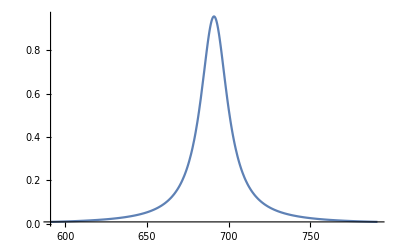

```mathematica
With[{a=20,b=10,c=10},Plot[3a/2*PDF[CauchyDistribution[defectFreqs[[1]][[1]],a/2],x],{x,-5a+defectFreqs[[1]][[1]],defectFreqs[[1]][[1]]+5a},PlotRange->All]]
```

```mathematica
ClearAll@x
```

```mathematica
defectLorentz=With[{a=25},Table[Table[3a/5*PDF[CauchyDistribution[defectFreqs[[j]][[i]],a],x],{i,1,defectFreqs[[j]]//Length}],{j,1,Length@defectFreqs}]]
```

{{3/(5 π (1+1/625 (-691+x)^2)),3/(5 π (1+1/625 (-791+x)^2)),3/(5 π (1+1/625 (-1092+x)^2))},{3/(5 π (1+1/625 (-374+x)^2)),3/(5 π (1+1/625 (-763+x)^2)),3/(5 π (1+1/625 (-816+x)^2)),3/(5 π (1+1/625 (-903+x)^2))},{3/(5 π (1+1/625 (-784+x)^2))},{3/(5 π (1+1/625 (-357+x)^2)),3/(5 π (1+1/625 (-811+x)^2)),3/(5 π (1+1/625 (-862+x)^2)),3/(5 π (1+1/625 (-1077+x)^2))},{3/(5 π (1+1/625 (-391+x)^2)),3/(5 π (1+1/625 (-691+x)^2)),3/(5 π (1+1/625 (-843+x)^2))}}

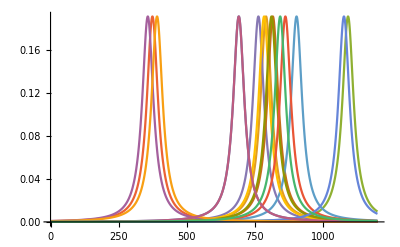

```mathematica
Plot[defectLorentz,{x,0,1200},PlotRange->All]
```